## Set up equations for all the potentials, and for lattice depth

### Define rotations ( x-axis along symmetry axis of dipole trap )

```mathematica
r90x=RotationTransform[π/2,{1,0,0}];
r90y=RotationTransform[π/2,{0,1,0}];
r90z=RotationTransform[π/2,{0,0,1}];
r15z=RotationTransform[π/12,{0,0,1}];
rpz=RotationTransform[π/24,{0,0,1}]; (*plus*)
rmz=RotationTransform[-π/24,{0,0,1}];  (*minus*)

rplattz=RotationTransform[3 π/8,{0,0,1}]; (*plus*)
rmlattz=RotationTransform[-π/8,{0,0,1}];  (*minus*)
rtlatt=RotationTransform[π/2,{0,1,0}]; (*top-bot *)
```

### Define rotations ( x-axis along one of the lattice beams )

```mathematica
r90x=RotationTransform[π/2,{1,0,0}];
r90y=RotationTransform[π/2,{0,1,0}];
r90z=RotationTransform[π/2,{0,0,1}];
r15z=RotationTransform[π/12,{0,0,1}];
rpz=RotationTransform[π/24+π/8,{0,0,1}]; (*plus*)
rmz=RotationTransform[-π/24+π/8,{0,0,1}];  (*minus*)

rplattz=RotationTransform[3 π/8+π/8,{0,0,1}]; (*plus*)
rmlattz=RotationTransform[-π/8+π/8,{0,0,1}];  (*minus*)
rtlatt=RotationTransform[π/2,{0,1,0}]; (*top-bot *)

rprobe=RotationTransform[π/6,{0,0,1}];
```

### Define trap geometry, depth is in units of recoil. fcpow specifies trap depth fraction at end of evap.

```mathematica
(*Single beam without back reflection*)
(*P in Watts,w0, and all lengths in microns,*)
(*usingle propagates along r[[1]]*)
U0[λ_]:=If[λ==1.064, -38709/1.4,If[λ==0.532,39561/1.4,ERROR],ERROR]
uone[λ_,P_,r_,w0_]:=U0[λ] P/w0^2( 1/(1+r[[1]]^2/((π w0^2/λ)^2)) Exp[-2(r[[2]]^2/w0^2+r[[3]]^2/w0^2)/(1+r[[1]]^2/((π w0^2/λ)^2))]);
uodt[P_,r_,w0_]:=uone[1.064,P[[1]],rpz[r],w0[[1]]]+uone[1.064,P[[2]],rmz[r]+{0,0,0},w0[[2]]];

(*The latest waists and powers are used here*)(*Dec 10,2012*)
w1=55.;
w2=55.;

(*Week of Jan 11,2013*)
P1=38.;
P2=38.;

odt[fcpow_,r_]:=uodt[{(fcpow /10.)P1,(fcpow/10.)P2},r,{w1,w2}];
```

### Define lattice geometry with rotators, depth is a function of Er α=1 is lattice, α=0 is dimple

```mathematica
uirLcr[scale_,P_,r_,w0_,R_,α_]:=

(4 Cos[(2 π rplattz[r][[1]])/(1.064 scale)]^2 √(R(α)) +1+R-2 √(R(α)))uone[1.064,P,rplattz[r],w0]+
(4 Cos[(2 π rmlattz[r][[1]])/(1.064 scale)]^2 √(R(α)) +1+R-2 √(R(α)))uone[1.064,P,rmlattz[r],w0]+(4 Cos[(2 π rtlatt[r][[1]])/(1.064 scale)]^2 √(R(α)) +1+R-2 √(R(α)))uone[1.064,P,rtlatt[r],w0]

irLcr[Er_,r_,α_]:=Module[{wir=42,scale=10,R=1,P},
P=1.4/38709(Er wir^2)/4;
uirLcr[scale,P,r,wir,R,α]]

uirLcrBot[scale_,P_,r_,w0_,R_,α_]:=
(4 √(R(α)) +1+R-2 √(R(α)))uone[1.064,P,rplattz[r],w0]+
(4 √(R(α)) +1+R-2 √(R(α)))uone[1.064,P,rmlattz[r],w0]+(4 √(R(α)) +1+R-2 √(R(α)))uone[1.064,P,rtlatt[r],w0]

irLcrBot[Er_,r_,α_]:=Module[{wir=42,scale=10,R=1,P},
P=1.4/38709(Er wir^2)/4;
uirLcrBot[scale,P,r,wir,R,α]]
```

### Define lattice geometry, depth is a function of Er

```mathematica
uir[scale_,P_,r_,w0_]:=
4 Cos[(2 π rplattz[r][[1]])/(1.064 scale)]^2 uone[1.064,P,rplattz[r],w0]+4 Cos[(2 π rmlattz[r][[1]])/(1.064 scale)]^2 uone[1.064,P,rmlattz[r],w0]+4 Cos[(2 π rtlatt[r][[1]])/(1.064 scale)]^2 uone[1.064,P,rtlatt[r],w0]

ir[Er_,r_]:=Module[{wir=42,scale=10,P},
P=1.4/38709(Er wir^2)/4;
uir[scale,P,r,wir]]

uirBot[scale_,P_,r_,w0_]:=
4 uone[1.064,P,rplattz[r],w0]+
4 uone[1.064,P,rmlattz[r],w0]+
4 uone[1.064,P,rtlatt[r],w0]

irBot[Er_,r_]:=Module[{wir=42,scale=10,P},
P=1.4/38709(Er wir^2)/4;
uirBot[scale,P,r,wir]]
```

### Define dimple geometry, depth is a function of Er

```mathematica
udimple[scale_,P_,r_,w0_]:=
2 uone[1.064,P,rplattz[r],w0]+2 uone[1.064,P,rmlattz[r],w0]+2 uone[1.064,P,rtlatt[r],w0]

dimple[Er_,r_]:=Module[{wir=42,scale=10,P},
P=1.4/38709(Er wir^2)/4;
udimple[scale,P,r,wir]]
```

### Define green geometry, depth is a function of Er

```mathematica
ugr[scale_,P_,r_,w0_]:=
uone[0.532,P,rplattz[r],w0]+
uone[0.532,P,rmlattz[r],w0]+
uone[0.532,P,rtlatt[r],w0]

gr[Er_,r_]:=Module[{wg=36,scale=10,P},
P=1.4/39461 Er wg^2;
ugr[scale,P,r,wg]]
```

### Define compensated geometry, depth is a function of Er (IR) and Er (GR)

```mathematica
comp[ErIR_,ErGR_,r_]:=ir[ErIR,r]+gr[ErGR,r]
compBot[ErIR_,ErGR_,r_]:=irBot[ErIR,r]+gr[ErGR,r]
compOdt[ErIR_,ErGR_,fcpow_,r_]:=ir[ErIR,r]+gr[ErGR,r]+odt[fcpow,r]
compOdtBot[ErIR_,ErGR_,fcpow_,r_]:=irBot[ErIR,r]+gr[ErGR,r]+odt[fcpow,r]
compDimple[ErIR_,ErGR_,fcpow_,r_]:=dimple[ErIR,r]+gr[ErGR,r]

compLcr[ErIR_,ErGR_,r_,α_]:=irLcr[ErIR,r,α]+gr[ErGR,r]
compLcrBot[ErIR_,ErGR_,r_,α_]:=irLcrBot[ErIR,r,α]+gr[ErGR,r]

compOdtLcr[ErIR_,ErGR_,fcpow_,r_,α_]:= irLcr[ErIR,r,α]+gr[ErGR,r]+odt[fcpow,r]
compOdtLcrBot[ErIR_,ErGR_,fcpow_,r_,α_]:=irLcrBot[ErIR,r,α]+gr[ErGR,r]+odt[fcpow,r]
```

### Define lattice depth as a function of position and as a function of LCR rotation α. Lattice depth is a vector, for the depth along each direction.

```mathematica
v0pos[v0_,r_,α_]:= Module[ {v0x,v0y,v0z,λ=1.064,w0=42,R=1},
v0x=v0[[1]] √(R(α))( 1/(1+r[[1]]^2/((π w0^2/λ)^2)) Exp[-2(r[[2]]^2/w0^2+r[[3]]^2/w0^2)/(1+r[[1]]^2/((π w0^2/λ)^2))]);
v0y=v0[[2]] √(R(α))( 1/(1+r[[2]]^2/((π w0^2/λ)^2)) Exp[-2(r[[3]]^2/w0^2+r[[1]]^2/w0^2)/(1+r[[2]]^2/((π w0^2/λ)^2))]);
v0z=v0[[3]] √(R(α))( 1/(1+r[[3]]^2/((π w0^2/λ)^2)) Exp[-2(r[[1]]^2/w0^2+r[[2]]^2/w0^2)/(1+r[[3]]^2/((π w0^2/λ)^2))]);
{v0x,v0y,v0z}]
```

### Get lattice depth at center for isotropic lattice, for a given rotation

```mathematica
v0[ErIR_,α_]:=Module[{R=1},ErIR √α]
```

### Define a function that plots lattice as a function of the distance along 111

```mathematica
latticeDiag[ErIR_,ErGR_,α_,x_]:=
Module[{r,scale=10},
r= {x/(√3),x/(√3),x/(√3)};
irLcrBot[ErIR,r,α]+gr[ErGR,r]+ v0pos[{ErIR,ErIR,ErIR},r,α] Cos[(2 π x)/(1.064 scale)]^2
]
```

### Define functions for easy plotting of potentials (function should be a function of x,y)

```mathematica
NicePlot1d[fun_,yrange_,range_]:=Module[
{plotpoints=80},
Plot[fun,{x,-range,range},PlotPoints->plotpoints,PlotRange->yrange,GridLines->Automatic,Frame->True,FrameLabel->{"μm","E_R"},LabelStyle->Directive[FontFamily->"Times",FontSize->18,Bold],ImageSize->{400}]
]
NicePlot[ fun_,ymin_,ymax_,range_]:=Module[
{plotpoints=80
},
DensityPlot[ fun, {x,-range,range},{y,-range,range},PlotPoints->plotpoints,PlotRange->{ymin,ymax},ColorFunctionScaling->True,ColorFunction->"AvocadoColors",FrameLabel->{"μm","μm"},LabelStyle->Directive[FontFamily->"Times",FontSize->18,Bold],ImageSize->{400}]]
```

## Calculate band structure as a function of position along 111 direction

### Define band structure as a function of lattice depth. Save tables of the evaluation of the band structure as a function of distance along 111

```mathematica
Clear[H];H[NPoints_,q_,V0_] := SparseArray[{{i_,i_}:>((q+2(i-1-NPoints))^2+V0/2), {i_,j_} /; i-j == 1 :>(V0/4),{i_,j_} /; i-j == -1:> (V0/4)},{2NPoints+1,2NPoints+1}] 
eigenval[NPoints_,q_,V0_,Band_]:=Sort[Eigenvalues[ H[NPoints,q,V0]]][[Band+1]]
eigenval3d[q_,v0_,Band_]:=Module[{NPoints,order,x,y,z, evals,bb,i,j,k},
NPoints=5; (*# of plane waves in each Bloch wave*)
order=Ordering[v0];
evals={Sort[Eigenvalues[ H[NPoints,q[[1]],v0[[1]]]]],Sort[Eigenvalues[ H[NPoints,q[[2]],v0[[2]]]]],Sort[Eigenvalues[ H[NPoints,q[[3]],v0[[3]]]]]};
bb=Band;i=1;j=1;k=1;
While[bb>0, i++; bb--;  If[bb>0,j++;bb--,None]; If[bb>0,k++;bb--,None]];
(*Print[i];
Print[j];
Print[k];
Print[evals];*)
evals[[order[[1]]]][[i]]+evals[[order[[2]]]][[j]]+evals[[order[[3]]]][[k]]
]

(*BOTTOM OF FIRST BAND ALONG 111*)
bot0=Flatten[Table[{{ErIR,α,x},Re[eigenval3d[{0.,0.,0.},v0pos[{ErIR,ErIR,ErIR},{x/(√3),x/(√3),x/(√3)},α],0]]},{ErIR,0.5,20,1.0},{α,0,1,0.1},{x,0,150,5.}],2];
bot0dat=bot0;

bot0plots=Timing[GraphicsGrid[{{ContourPlot[eigenval3d[{0.,0.,0.},v0pos[{ErIR,ErIR,ErIR},{x/(√3),x/(√3),x/(√3)},0.],0],{x,0,100},{ErIR,1,12}],ContourPlot[eigenval3d[{0.,0.,0.},v0pos[{ErIR,ErIR,ErIR},{x/(√3),x/(√3),x/(√3)},1.],0],{x,0,100},{ErIR,1,12}],Plot[eigenval3d[{0.,0.,0.},v0pos[{ErIR,ErIR,ErIR},{x/(√3),x/(√3),x/(√3)},1.],0]/.ErIR->6.,{x,0,100}]}}]];


(*TOP OF FIRST BAND ALONG 111*)
top0=Flatten[Table[{{ErIR,α,x},Re[eigenval3d[{1.,1.,1.},v0pos[{ErIR,ErIR,ErIR},{x/(√3),x/(√3),x/(√3)},α],0]]},{ErIR,0.5,20,1.0},{α,0,1,0.1},{x,0,150,5.}],2];
top0dat=top0;

top0plots=Timing[GraphicsGrid[{{ContourPlot[eigenval3d[{1.,1.,1.},v0pos[{ErIR,ErIR,ErIR},{x/(√3),x/(√3),x/(√3)},0.],0],{x,0,100},{ErIR,1,12}],ContourPlot[eigenval3d[{1.,1.,1.},v0pos[{ErIR,ErIR,ErIR},{x/(√3),x/(√3),x/(√3)},1.],0],{x,0,100},{ErIR,1,12}],Plot[eigenval3d[{1.,1.,1.},v0pos[{ErIR,ErIR,ErIR},{x/(√3),x/(√3),x/(√3)},1.],0]/.ErIR->6,{x,0,100}]}}]];



(*BOTTOM OF SECOND BAND ALONG 111*)
bot1=Flatten[Table[{{ErIR,α,x},Re[eigenval3d[{1.,0.,0.},v0pos[{ErIR,ErIR,ErIR},{x/(√3),x/(√3),x/(√3)},α],1]]},{ErIR,0.5,20,1.0},{α,0,1,0.1},{x,0,150,5.}],2];
bot1dat=bot1;

bot1plots=Timing[GraphicsGrid[{{ContourPlot[eigenval3d[{1.,0.,0.},v0pos[{ErIR,ErIR,ErIR},{x/(√3),x/(√3),x/(√3)},0.],1],{x,0,100},{ErIR,1,12}],ContourPlot[eigenval3d[{1.,0.,0.},v0pos[{ErIR,ErIR,ErIR},{x/(√3),x/(√3),x/(√3)},1.],1],{x,0,100},{ErIR,1,12}],Plot[eigenval3d[{1.,0.,0.},v0pos[{ErIR,ErIR,ErIR},{x/(√3),x/(√3),x/(√3)},1.],1]/.ErIR->6.,{x,0,100}]}}]];

(*TOP OF SECOND BAND ALONG 111*)
top1=Flatten[Table[{{ErIR,α,x},Re[eigenval3d[{0.,0.,0.},v0pos[{ErIR,ErIR,ErIR},{x/(√3),x/(√3),x/(√3)},α],1]]},{ErIR,0.5,20,1.0},{α,0,1,0.1},{x,0,150,5.}],2];
top1dat=top1;

top1plots=Timing[GraphicsGrid[{{ContourPlot[eigenval3d[{0.,0.,0.},v0pos[{ErIR,ErIR,ErIR},{x/(√3),x/(√3),x/(√3)},0.],1],{x,0,100},{ErIR,1,12}],
ContourPlot[eigenval3d[{0.,0.,0.},v0pos[{ErIR,ErIR,ErIR},{x/(√3),x/(√3),x/(√3)},1.],1],{x,0,100},{ErIR,1,12}],Plot[eigenval3d[{0.,0.,0.},v0pos[{ErIR,ErIR,ErIR},{x/(√3),x/(√3),x/(√3)},1.],1]/.ErIR->6.,{x,0,100}]}}]];

SetDirectory[NotebookDirectory[]];
DumpSave["bands.mx",{bot0dat,bot0plots,top0dat,top0plots,bot1dat,bot1plots,top1dat,top1plots}];
```

## Get interpolation data for band structure as a function of position along 111 direction

```mathematica
SetDirectory[NotebookDirectory[]];
Clear[bot0dat,bot0plots,top0dat,top0plots,bot1dat,bot1plots,top1dat,top1plots];
<<bands.mx
fbot0=Interpolation[bot0dat];
ftop0=Interpolation[top0dat];
fbot1=Interpolation[bot1dat];
ftop1=Interpolation[top1dat];
```

## Test interpolation data for band structure as a function of position along 111 direction

BOTTOM OF FIRST BAND ALONG 111

Interpolation :  0.124007 Seconds

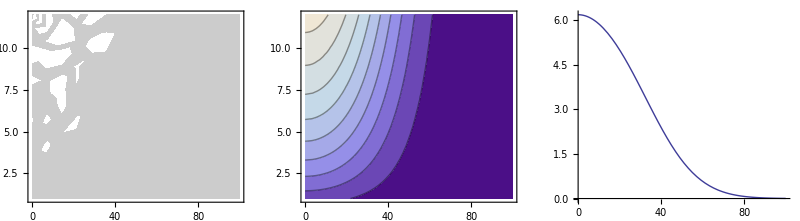

Calculation :  76.800799 Seconds

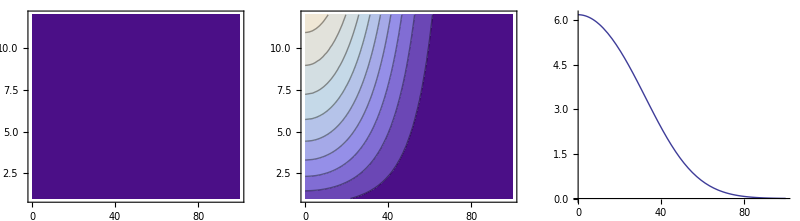

TOP OF FIRST BAND ALONG 111

Interpolation :  0.072004 Seconds

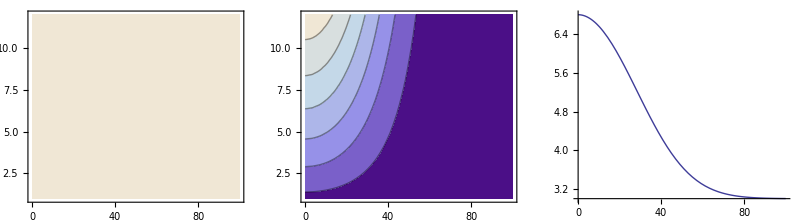

Calculation :  74.436652 Seconds

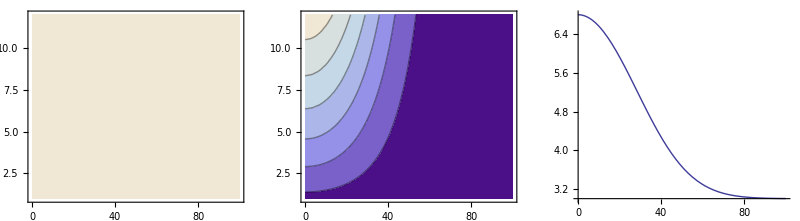

BOTTOM OF SECOND BAND ALONG 111

Interpolation :  0.076005 Seconds

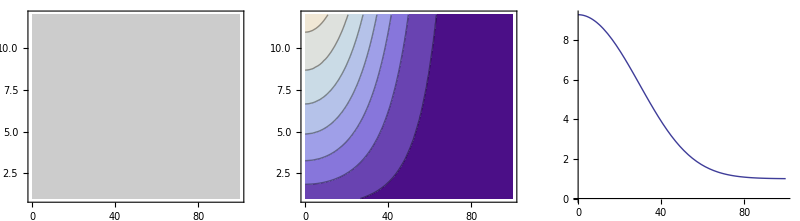

Calculation :  130.728169 Seconds

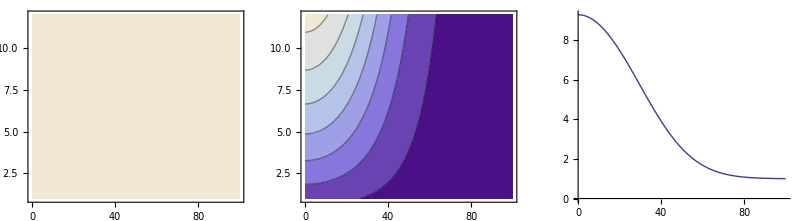

TOP OF SECOND BAND ALONG 111

Interpolation :  0.068005 Seconds

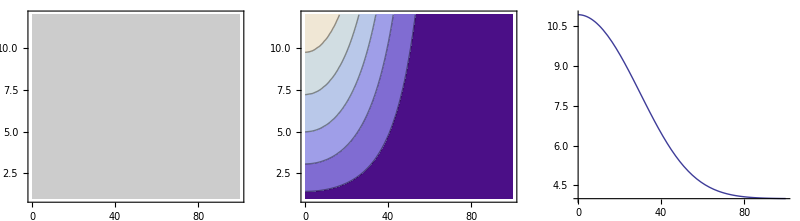

Calculation :  74.312644 Seconds

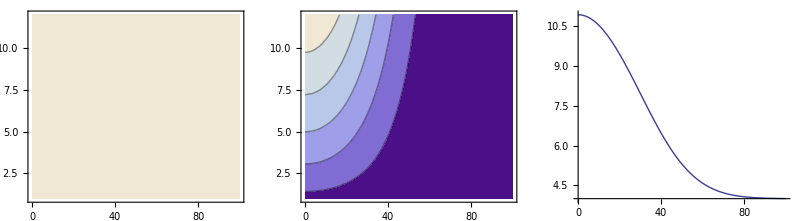

```mathematica
imsize=800;

TextCell["BOTTOM OF FIRST BAND ALONG 111","Subsection"]
out=Timing[GraphicsGrid[{{ContourPlot[fbot0[ErIR,0,x],{x,0,100},{ErIR,1,12}],ContourPlot[fbot0[ErIR,1.,x],{x,0,100},{ErIR,1,12}],Plot[fbot0[ErIR,1.,x]/.ErIR->6.,{x,0,100}]}}, ImageSize->imsize]];

TextCell["Interpolation :  "<>ToString[out[[1]]]<>" Seconds","Subsubsection"]
Show[out[[2]]]
TextCell["Calculation :  "<>ToString[bot0plots[[1]]]<>" Seconds","Subsubsection"]
Show[bot0plots[[2]],ImageSize->imsize]



TextCell["TOP OF FIRST BAND ALONG 111","Subsection"]
out=Timing[GraphicsGrid[{{ContourPlot[ftop0[ErIR,0,x],{x,0,100},{ErIR,1,12}],ContourPlot[ftop0[ErIR,1.,x],{x,0,100},{ErIR,1,12}],Plot[ftop0[ErIR,1.,x]/.ErIR->6.,{x,0,100}]}}, ImageSize->imsize]];

TextCell["Interpolation :  "<>ToString[out[[1]]]<>" Seconds","Subsubsection"]
Show[out[[2]]]
TextCell["Calculation :  "<>ToString[top0plots[[1]]]<>" Seconds","Subsubsection"]
Show[top0plots[[2]],ImageSize->imsize]

TextCell["BOTTOM OF SECOND BAND ALONG 111","Subsection"]
out=Timing[GraphicsGrid[{{ContourPlot[fbot1[ErIR,0,x],{x,0,100},{ErIR,1,12}],ContourPlot[fbot1[ErIR,1.,x],{x,0,100},{ErIR,1,12}],Plot[fbot1[ErIR,1.,x]/.ErIR->6.,{x,0,100}]}}, ImageSize->imsize]];

TextCell["Interpolation :  "<>ToString[out[[1]]]<>" Seconds","Subsubsection"]
Show[out[[2]]]
TextCell["Calculation :  "<>ToString[bot1plots[[1]]]<>" Seconds","Subsubsection"]
Show[bot1plots[[2]],ImageSize->imsize]


TextCell["TOP OF SECOND BAND ALONG 111","Subsection"]
out=Timing[GraphicsGrid[{{ContourPlot[ftop1[ErIR,0,x],{x,0,100},{ErIR,1,12}],ContourPlot[ftop1[ErIR,1.,x],{x,0,100},{ErIR,1,12}],Plot[ftop1[ErIR,1.,x]/.ErIR->6.,{x,0,100}]}}, ImageSize->imsize]];

TextCell["Interpolation :  "<>ToString[out[[1]]]<>" Seconds","Subsubsection"]
Show[out[[2]]]
TextCell["Calculation :  "<>ToString[top1plots[[1]]]<>" Seconds","Subsubsection"]
Show[top1plots[[2]],ImageSize->imsize]
```

## Define band structure functions

### Define functions that give bottom and top of band as a function of position. The three lattice beams are assumed to have the same depth v0 at r={0,0,0}.

```mathematica
bandBot[ErIR_,ErGR_,α_,x_]:=fbot0[ErIR,α,Abs[x]]+compLcrBot[ErIR,ErGR,1/(√3){x,x,x},α]
bandTop[ErIR_,ErGR_,α_,x_]:=ftop0[ErIR,α,Abs[x]]+compLcrBot[ErIR,ErGR,1/(√3){x,x,x},α]
band1Bot[ErIR_,ErGR_,α_,x_]:=fbot1[ErIR,α,Abs[x]]+compLcrBot[ErIR,ErGR,1/(√3){x,x,x},α]
band1Top[ErIR_,ErGR_,α_,x_]:=ftop1[ErIR,α,Abs[x]]+compLcrBot[ErIR,ErGR,1/(√3){x,x,x},α]
(*gravity[x_]:=1/(√3)x (0.00505)*)
```

### Define function to make a nice plot of the band for a given IR, GR, and ALPHA

```mathematica
band[ErIR_,ErGR_,α_]:=Module[{x},
Plot[
{bandBot[ErIR,ErGR,α,√3 x 0.532] ,bandTop[ErIR,ErGR,α,√3 x 0.532],band1Bot[ErIR,ErGR,α,√3 x 0.532] ,band1Top[ErIR,ErGR,α,√3 x 0.532],latticeDiag[ErIR,ErGR,α,√3 x 0.532]},{x,-100,100},
Filling->{1->{2},3->{4}},
GridLines->Automatic,
Frame->True,
FrameStyle->Thickness[0.005],
FrameLabel->{"Distance from center along 111 (√3d) ","E_R"},
LabelStyle->Directive[FontFamily->"Times",FontSize->14,Bold],ImageSize->{380},AspectRatio-> 1.2,PlotRange->{-10,5},Epilog->Text[StandardForm[PadLeft[Characters["IR="],6," "]<>PadLeft[Characters[ToString[NumberForm[ErIR,{4,3}]]],6," "]<>"\n"<>PadLeft[Characters["GR="],6," "]<>PadLeft[Characters[ToString[NumberForm[ErGR,{4,3}]]],6," "]<>"\n"<>PadLeft[Characters["α="],6," "]<>PadLeft[Characters[ToString[NumberForm[α,{4,3}]]],6," "]],{50,-8.5}]
]
]
```

## Plot some example potentials

```mathematica
GraphicsGrid[{{NicePlot[ compOdtLcr[0.,0., 0.085,{x,y,0},0.],-100,100,80], 
NicePlot[compOdtLcr[4.4,0., 0.085,{x,y,0},0.],-100,100,80],
NicePlot[compOdtLcr[4.4,0., 0.085,{x,y,0},1.],-100,100,80]}}]
```

-Graphics-

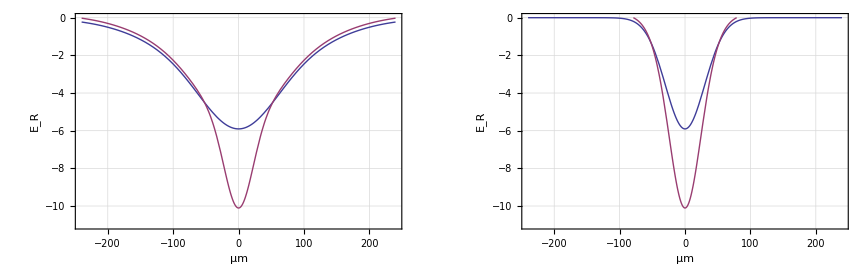

```mathematica
offset=2.4;
ymin=-11.;
GraphicsGrid[ {{ NicePlot1d[{ compOdtLcr[0.,0.,0.085,{x,0,0},0.], offset+compOdtLcr[4.4,0.,0.085,{x,0,0},0.]}, {ymin,0},240] , NicePlot1d[{ compOdtLcr[0.,0.,0.085,{0,x,0},0.], offset+ compOdtLcr[4.4,0.,0.085,{0,x,0},0.]},{ymin,0},240] }}]
```

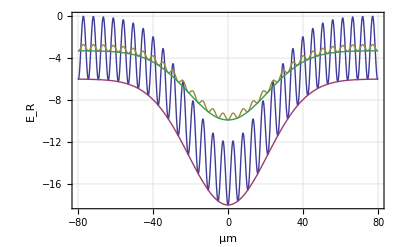

```mathematica
NicePlot1d[{compLcr[6.,0.,{x,0,0},1.],compLcrBot[6.,0.,{x,0,0},1.],compLcr[6.,0.,{x,0,0},1/100.],compLcrBot[6.,0.,{x,0,0},1/100.]},Automatic,80]
```

## Plot some example band structures

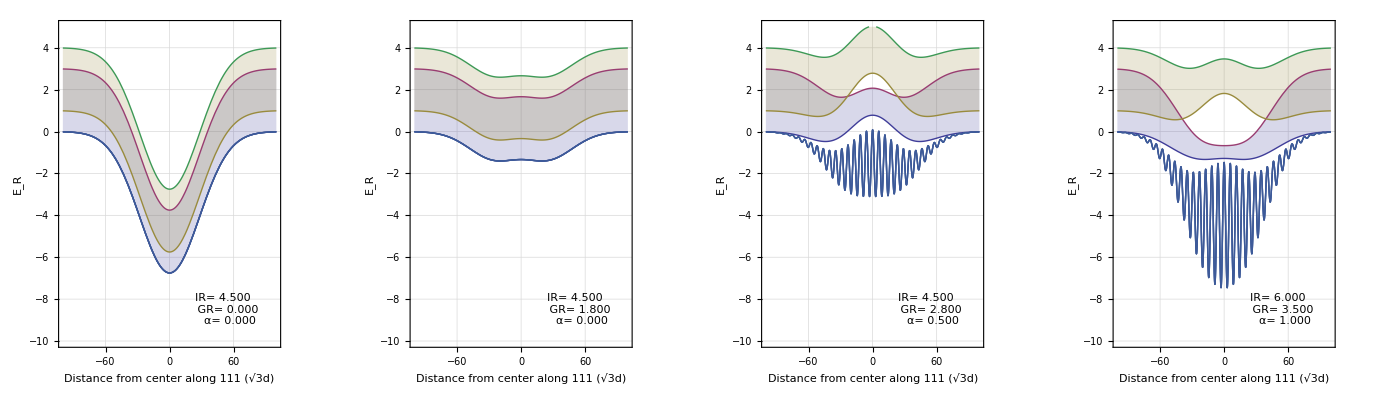

```mathematica
GraphicsGrid[{{band[4.5,0,0.],band[4.5,1.8,0.],band[4.5,2.8,0.5],band[6.,3.5,1.]}}]
```

## Save table to interpolate the bottom and top of the first and second bands as a function of ErIR, ErGR, α

```mathematica
Module[{head,stream,dat},
dat=Table[ N[{ErIR, ErGR, α, bandBot[ErIR, ErGR, α,0.],bandTop[ErIR, ErGR, α,0.],band1Bot[ErIR, ErGR, α,0.],band1Top[ErIR, ErGR, α,0.]},6], {ErIR,0.5,18.,0.5},{ErGR,0.,18,0.5},{α,0.,1.,0.1}];
dat=Flatten[dat,2];
SetDirectory[NotebookDirectory[]];
head="#ErIR\tErGR\talpha\tband0Bot\tband0Top\tband1Bot\tband1Top\n";
stream=OpenWrite["bandData.dat"];
WriteString[stream,head<>ExportString[dat,"Table"]];
Close[stream];]
```

## Band flatness optimization

### Optimize shape of band bottom to go from ALPHA=0 (dimple) to ALPHA=1 (lattice)

```mathematica
optTrap[α_]:=Module[{IR,GR,x},
desired=Table[ {x,bandBot[6.,3.5,1.,√3 x 0.532]},{x,0,100,1}];
trial=bandBot[IR,GR,α,√3 x 0.532];
fit=FindFit[desired,trial,{{IR,4.5},{GR,1.8}},x];
{IR,GR}/.fit
]
optimal=Table[{α,optTrap[α]},{α,0,1,0.05}];
sequence=Table[{band[optimal[[i]][[2]][[1]],optimal[[i]][[2]][[2]],optimal[[i]][[1]]]},{i,1,Length[optimal],1}];
ListAnimate[Flatten[sequence]]
```

### Express optimal IR, GR, and α as a function of lattice depth, fit those functions using a third degree polynomial and DumpSave them for later use

```mathematica
optIR=Table[{v0[optimal[[i]][[2]][[1]],optimal[[i]][[1]]],optimal[[i]][[2]][[1]]},{i,1,Length[optimal],1}];
optGR=Table[{v0[optimal[[i]][[2]][[1]],optimal[[i]][[1]]],optimal[[i]][[2]][[2]]},{i,1,Length[optimal],1}];
optAL=Table[{v0[optimal[[i]][[2]][[1]],optimal[[i]][[1]]],optimal[[i]][[1]]},{i,1,Length[optimal],1}];



SetDirectory[NotebookDirectory[]];
DumpSave["optimalLoad.mx",{optIR, optGR, optAL}];
```

## Retrieve optimization results

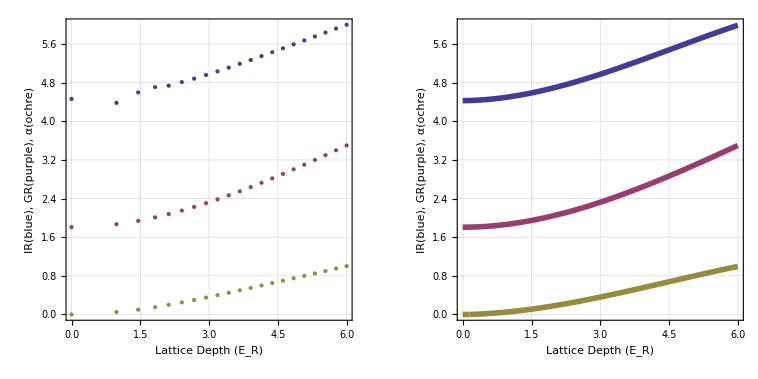

```mathematica
SetDirectory[NotebookDirectory[]];
<<optimalLoad.mx

Clear[optIRf,optGRf,optALf,x];
optIRf=Fit[optIR,{1,x,x^2,x^3},x];
optGRf=Fit[optGR,{1,x,x^2,x^3},x];
optALf=Fit[optAL,{1,x,x^2,x^3},x];

optIRfun[v0_]:=optIRf/.{x->v0}
optGRfun[v0_]:=optGRf/.{x->v0}
optALfun[v0_]:=Max[Min[1.0,optALf/.{x->v0}],0.]

optimalList=ListPlot[{optIR,optGR,optAL},GridLines->Automatic,Frame->True,FrameStyle->Thickness[0.005],FrameLabel->{"Lattice Depth (E_R)","IR(blue), GR(purple), α(ochre)"},LabelStyle->Directive[FontFamily->"Times",FontSize->14,Bold],ImageSize->{350},AspectRatio-> 1.,PlotRange->{0,6}];

optimalPlot=Plot[{optIRfun[x],optGRfun[x],optALfun[x]},{x,0.,6.},GridLines->Automatic,Frame->True,FrameStyle->Thickness[0.005],FrameLabel->{"Lattice Depth (E_R)","IR(blue), GR(purple), α(ochre)"},LabelStyle->Directive[FontFamily->"Times",FontSize->14,Bold],ImageSize->{350},AspectRatio-> 1.,PlotRange->{0,6},PlotStyle->{Thickness[0.01]}];

GraphicsGrid[{{optimalList,optimalPlot}}]
```

## Define the lattice depth ramp-up curve, and from it derive the curves for IR, GR, and ALPHA, plot full movie

```mathematica
tanhRise[x_]:=Module[{
v0=0,
vf=6,
dt=300,
tau=50,
shift=180},
v0+(vf-v0)(1+Tanh[(x-shift)/tau]-(1+Tanh[-shift/tau]))/(1+Tanh[(dt-shift)/tau]-(1+Tanh[-shift/tau]))]

rampPlot[time_]:=Plot[
{tanhRise[t],optIRfun[tanhRise[t]],optGRfun[tanhRise[t]],optALfun[tanhRise[t]]},{t,0.,300.},
GridLines->Automatic,
Frame->True,
FrameStyle->Thickness[0.005],
FrameLabel->{"time (ms)","Lattice depth (E_R)"},
LabelStyle->Directive[FontFamily->"Times",FontSize->14,Bold],
ImageSize->{350},
AspectRatio->0.8,
PlotRange->{0,6},
PlotStyle->{Directive[Thickness[0.02],ColorData[1,1]],
Directive[Thickness[0.01],ColorData[1,2]],
Directive[Thickness[0.01],ColorData[1,3]],
Directive[Thickness[0.01],ColorData[1,4]]},
Epilog->{Red,PointSize[0.04],Point[{time,tanhRise[time]}]}]

fullout[time_]:=
GraphicsGrid[{{
band[optIRfun[tanhRise[time]],optGRfun[tanhRise[time]],optALfun[tanhRise[time]] ],
rampPlot[time] }}]

sequence=Table[fullout[time],{time,0.,300.,25.}];
ListAnimate[sequence]
```

```mathematica
Export["latticeSequence.GIF",sequence,"DisplayDurations"->0.5, "AnimationRepetitions"->3,"ImageSize"->1000]
```

latticeSequence.GIF

## Older stuff

### Define function to make plot of dimple

```mathematica
dimplePlot[ErIR_,ErGR_,fcpow_,ErIRd_,ErGRd_,fcpowd_]:=Module[{coord,x},
coord=0.532{x,x,x};
Plot[{bandBot[ErIR,ErGR,fcpow,coord] ,bandTop[ErIR,ErGR,fcpow,coord],band1Bot[ErIR,ErGR,fcpow,coord] ,band1Top[ErIR,ErGR,fcpow,coord],latticeDiag[ErIR,ErGR,fcpow,√3 x 0.532],compDimple[ErIRd,ErGRd,fcpowd,coord] },{x,-100,100},Filling->{1->{2},3->{4}},PlotStyle->{Automatic,Automatic,Automatic,Automatic,Automatic,Directive[Thickness[0.015],ColorData[1,1]]},GridLines->Automatic,Frame->True,FrameStyle->Thickness[0.005],FrameLabel->{"Distance from center along 111 (√3d) ","E_R"},LabelStyle->Directive[FontFamily->"Times",FontSize->18,Bold],ImageSize->{400},AspectRatio-> 1.2,PlotRange->{-10,5}]
]
```

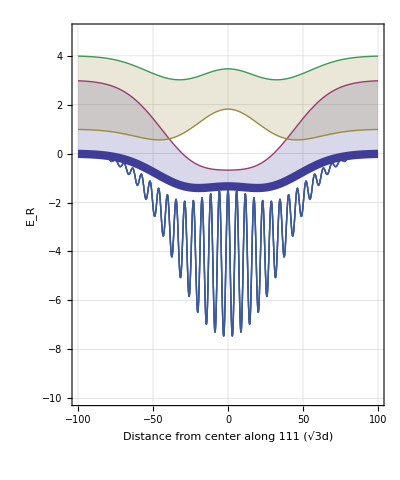

```mathematica
d0=dimplePlot[6.,3.5,0.,   4.5,1.8,0.0]
```

```mathematica
Export["6IR_3p5GR+dimple_4p5IR_1p8GR.png",d0,ImageResolution->240]
```

6IR_3p5GR+dimple_4p5IR_1p8GR.png

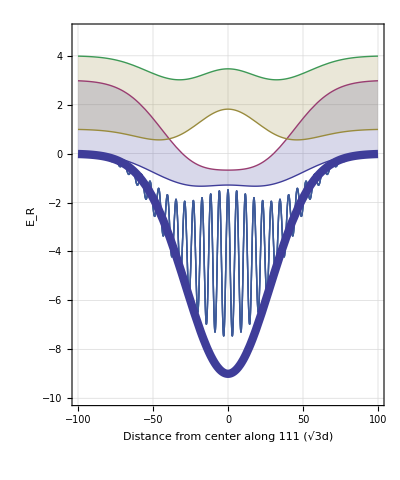

```mathematica
d1=dimplePlot[6.,3.5,0.,   6,0,0.0]
```

```mathematica
Export["6IR_3p5GR+dimple_6IR_0GR.png",d1,ImageResolution->240]
```

6IR_3p5GR+dimple_6IR_0GR.png

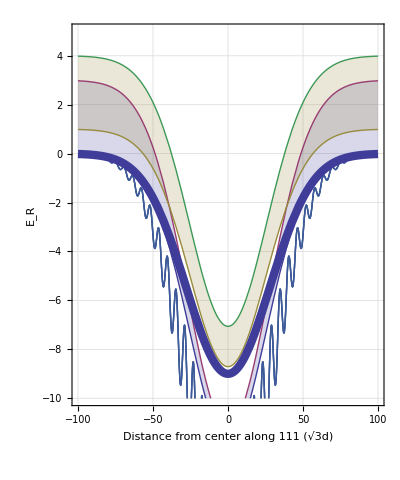

```mathematica
d2=dimplePlot[6.,0,0.,   6.,0,0.0]
```

```mathematica
Export["6IR_0GR+dimple_6IR_0R.png",d2,ImageResolution->240]
```

6IR_0GR+dimple_6IR_0R.png

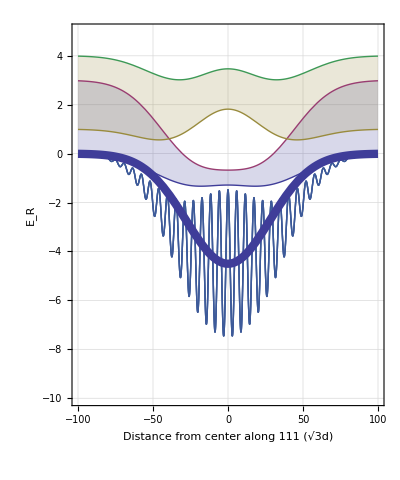

```mathematica
d3=dimplePlot[6.,3.5,0.,   3,0,0.0]
```

```mathematica
Export["6IR_3p5GR+dimple_3IR_0R.png",d3,ImageResolution->240]
```

6IR_3p5GR+dimple_3IR_0R.png

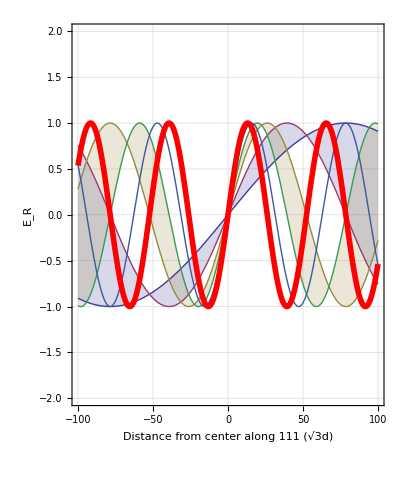

```mathematica
Plot[{Sin[x/50],Sin[2x/50],Sin[3x/50] ,Sin[4x/50],Sin[5x/50],Sin[6x/50] },{x,-100,100},Filling->{1->{2},3->{4}},PlotStyle->{Automatic,Automatic,Automatic,Automatic,Automatic,Directive[Thickness[0.01],Red]},GridLines->Automatic,Frame->True,FrameLabel->{"Distance from center along 111 (√3d) ","E_R"},LabelStyle->Directive[FontFamily->"Times",FontSize->18,Bold],ImageSize->{400},AspectRatio-> 1.2,PlotRange->{-2,2}]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

H:\pedro\apparatus3\1108-antilattice\potentials

```mathematica
Export["compensated_10_6p8_0.05_two_bands.png",%%%]
```

compensated_10_6p8_0.05_two_bands.png

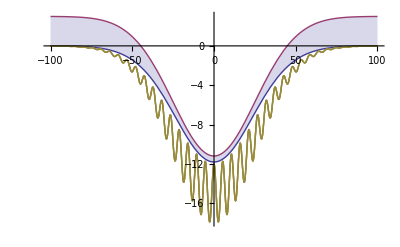

```mathematica
band[6.,0.,0.]
```

```mathematica
compensated[ErIR_]:=Table[band[ErIR,ErGR,0.0],{ErGR,{0.,0.33 ErIR,0.66 ErIR, ErIR}}]
```

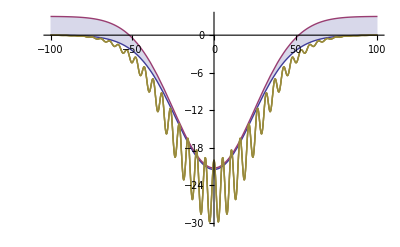
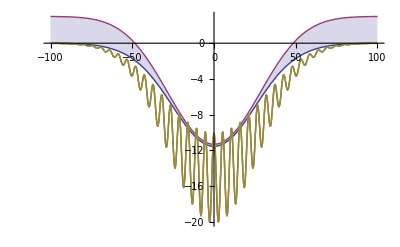
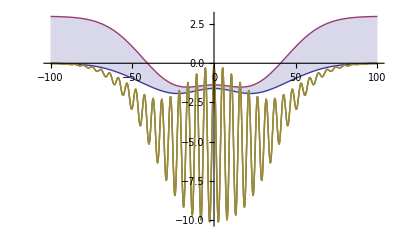
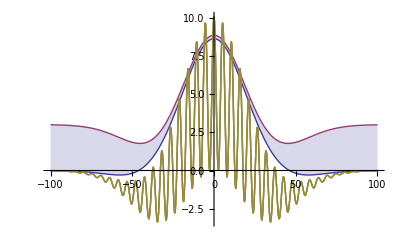

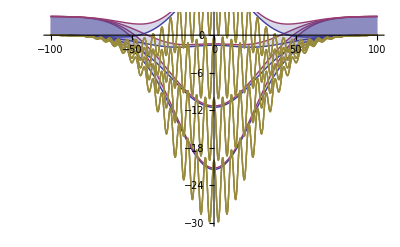

```mathematica
c10=compensated[10]
Show[c10]
```

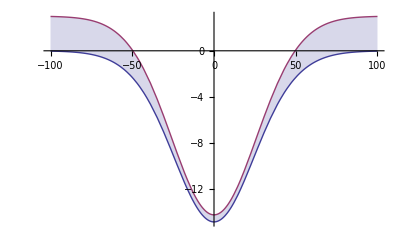
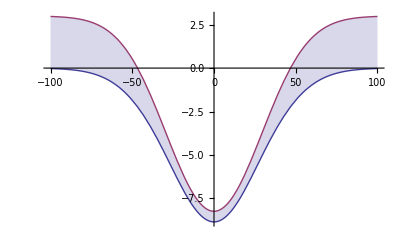
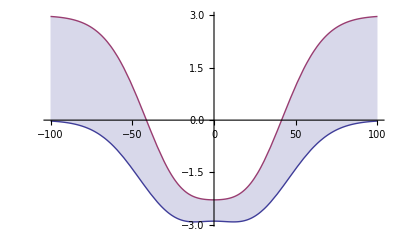
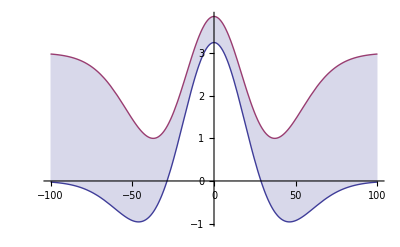

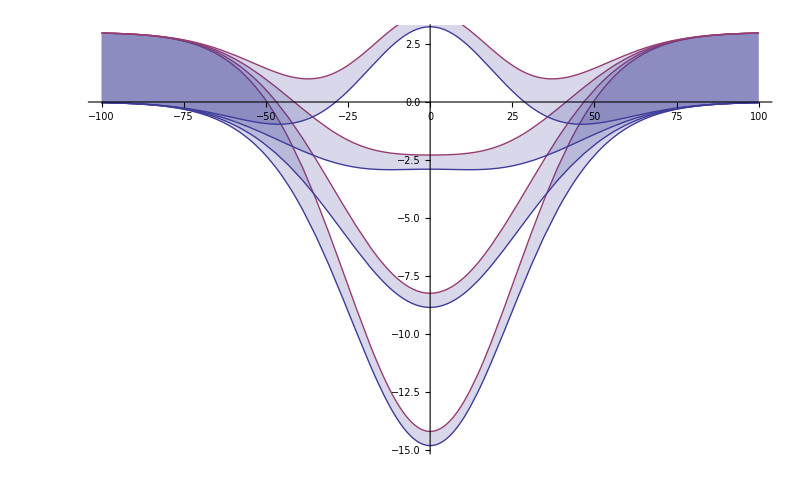

```mathematica
c6=compensated[6]
Show[c6]
```

### Gravity in units of recoil per micrometer

Mass of lithium is 9.96e-27 kg
Acceleration of gravity is 9.8 m/s^2 = 980 cm/s^2

mgh = Er = kb (1.4 uK)

kb/m = 13.85 cm^2 / s^2 / uK

so  h  =  ( 13.85 cm^2 / s^2 / uK ) ( 1.4 uK ) / g =  ( 19.39 / 980 ) cm =  1.979 e-2 cm = 197.9 um 

Therefore in recoils per micrometer the potential of gravity on a lihtium atom is 

gravity  = 5.05e-3 Er/um